-0.0048

{{y[x]→0.333868 x^2}}

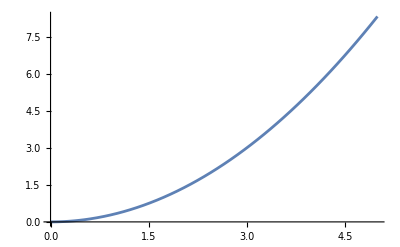

```mathematica
tau = -0.0048
Clear[y];
solution = DSolve[{y'[x]==-3*y[x] + x^2, y[0]==0},y[x],x]
Plot[y[x]/.solution,{x,0,5}]
```